```mathematica
EeFlux[Enu_]:=192/mMu*(Enu/mMu)^2(1/2 - Enu/mMu)
```

```mathematica
F[Er_]:=1
```

```mathematica
XSection[Enu_,Er_]:=GF^2*M/(Pi) ((Gv+Ga)^2+(Gv-Ga)^2(1-Er/Enu)^2-(Gv^2-Ga^2)M Er/Enu^2)
```

```mathematica
Gv:=0.0298*55-0.5117*78
```

```mathematica
Ga:=0
```

```mathematica
M:=123800.645
```

```mathematica
GF :=1.16637*^-11
```

```mathematica
mMu := 105.6583755
```

```mathematica
eRSpectrum[Er_]:=Integrate[EeFlux[ENu]*XSection[ENu,Er],{ENu, Sqrt[M*Er/2], mMu/2}]
```

```mathematica
eRSpectrum[x]
```

7.07729×10^9-9.42078×10^11 x+5.91391×10^12 x^(3/2)-1.04264×10^13 x^2-5.60437×10^10 x^(5/2)+1.68727×10^8 x^3

```mathematica
eRSpectrum[0.03]
```

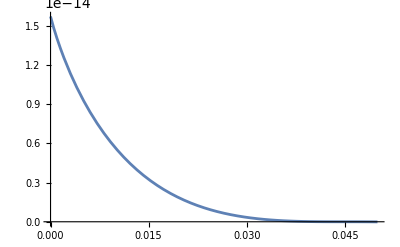

```mathematica
Plot[eRSpectrum[x],{x,0,0.05}]
```